```mathematica
Needs["Histograms`"]
```

FrequencyData::shdw: Symbol "FrequencyData" appears in multiple contexts {"Histograms`", "Global`"}; definitions in context "Histograms`" may shadow or be shadowed by other definitions.

Histogram::shdw: Symbol "Histogram" appears in multiple contexts {"Histograms`", "Global`"}; definitions in context "Histograms`" may shadow or be shadowed by other definitions.

```mathematica
data =Flatten[Import["/Users/Aline/Documents/WORK/LOA/Radioprotection/python/stats.csv"]];
```

```mathematica
Head[data]
```

List

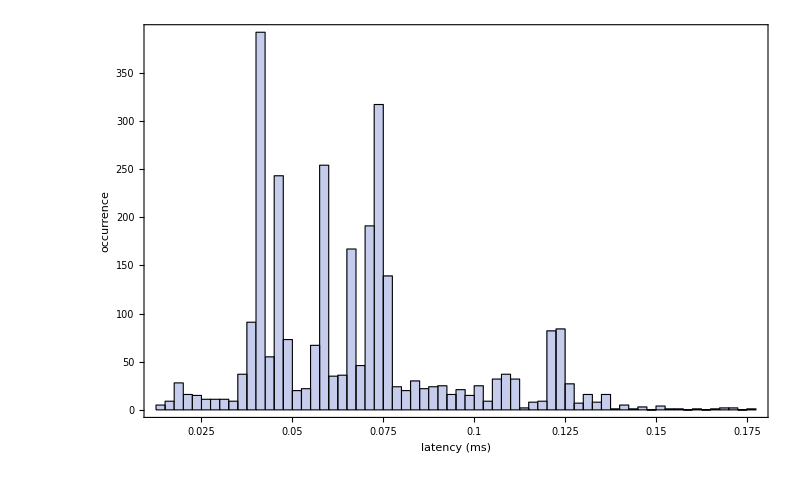

```mathematica
dat = Histogram[data 10^3, Frame-> True, FrameLabel->{{"occurrence",""},{"latency (ms)",""}}, ImageSize-> 800, BaseStyle-> {FontSize-> 25, FrameStyle-> {Thick}}]
```

```mathematica
Export["/Users/Aline/Documents/WORK/LOA/Radioprotection/python/stats.jpg" ,dat]
```

/Users/Aline/Documents/WORK/LOA/Radioprotection/python/stats.jpg